### init

```mathematica
SetOptions[#,
AxesStyle->Directive[Black,AbsoluteThickness[0.9]],
LabelStyle->Directive[Black,FontFamily->"CMU Serif",FontSize->16],
Frame->True,
FrameStyle->Directive[Black,AbsoluteThickness[0.9]],
FrameTicksStyle->Directive[Black,AbsoluteThickness[0.9],FontFamily->"CMU Serif",FontSize->13,FontSlant->Plain],
PlotRangePadding->{None,Automatic},
ImageSize->400
]&/@{Plot,LogPlot,LogLogPlot,LogLinearPlot,ListPlot,ListLogPlot,ListLogLogPlot,ListLogLinearPlot,ListLinePlot};
```

```mathematica
SetOptions[#,
FrameStyle->Directive[Black,AbsoluteThickness[0.9]]
]&/@{Framed};
```

```mathematica
Attributes[myStyle]={Listable};
SetAttributes[myStyle,HoldAllComplete];
myStyle[form_,others___]:=Style[TraditionalForm[HoldForm[form]],others,FontFamily->"CMU Serif"];
```

### data

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
filename="Data/MICROSCOPE/limits_MICROSCOPE.txt";
Get[filename];
```

```mathematica
σLZ=4.0*10^-33;
σSK=4.3*10^-32;
σPandaX=6.4*10^-32;
σCDEX=1.9*10^-30;
σSupernovaUpper1=1.2*10^-43;
σSupernovaUpper2=4.7*10^-42;
σSupernovaLower=6.12*^-46;
(*σRG=3*^-43;*)
σHB=2.77*^-37;

limitMICROSCOPEMassinkeV=Times[#,{10^-3,1}]&/@limitMICROSCOPE;
limitMICROSCOPEMassinkeV={{10^-3,limitMICROSCOPEMassinkeV[[1,2]]}}~Join~limitMICROSCOPEMassinkeV;
```

```mathematica
δnSquareBarMICROSCOPE=(7.29*10^22 cm^-3)^2;
nBarMICROSCOPE=2.688*10^24 cm^-3;
δaMICROSCOPE=4.8×10^−12;
δnSquareBarTB=(5.80*10^24 cm^-3)^2;
nBarTB=5.80*10^24 cm^-3;
δaTB=4.72×10^−13;
MICROSCOPE2TB=δaTB/δaMICROSCOPE(δnSquareBarTB/δnSquareBarMICROSCOPE)^-1;

limitProjTBMassinkeV2=Times[#,{1,MICROSCOPE2TB}]&/@limitMICROSCOPEMassinkeV;
```

### Fig2

```mathematica
<<MaTeX`;

(*tickForm[x_]:=If[StringQ[x],Text[Style[x,13,FontFamily->"CMU Serif"]],x];*)
myRange10[min_,max_]:=Module[{list},
list=10^Subdivide[Log[10,min],Log[10,max],Log[10,max/min]];
(Join@@Table[Range[list[[ii]],list[[ii+1]],list[[ii]]],{ii,Length[list]-1}])//DeleteDuplicates
];

longTick=0.015;
shortTick=1/2 longTick;

vTicks=myRange10[10^-50,10^-20];
leftTicks={
#,
If[Mod[Log[10,#],2]==0,myStyle[10]^myStyle[Log[10,#]]//ReleaseHold,Null],
If[Mod[Log[10,#],1]==0,longTick,shortTick]
}&/@(vTicks);
rightTicks={
#,
Null,
If[Mod[Log[10,#],1]==0,longTick,shortTick]
}&/@(vTicks);

hTicks=myRange10[10^-10,10^10];
bottomTicks={
#,
If[Mod[Log[10,#],1]==0,myStyle[10]^myStyle[Log[10,#]]//ReleaseHold,Null],
If[Mod[Log[10,#],1]==0,longTick,shortTick]
}&/@(hTicks);
topTicks={
#,
Null,
If[Mod[Log[10,#],1]==0,longTick,shortTick]
}&/@(hTicks);
```

```mathematica
frameLabel=MaTeX[#,FontSize->15]&/@{"m_\\chi \, [ \\mathrm{keV} ]","\\sigma_{\\chi N} \, [\\mathrm{cm}^{2}]"};
legendLabel=MaTeX[#,FontSize->9]&/@{"\\text{LUX-ZEPLIN}","\\text{Super-K}","\\text{PandaX-II}","\\text{CDEX-10}","\\text{Supernova Cooling}"};
MICROSCOPELabel=MaTeX["\\textbf{MICROSCOPE}",FontSize->16];
```

```mathematica
myColor1=RGBColor["#d5674f"]
myColor2=RGBColor["#4584D9"]
myColor3=RGBColor["#e48a00"]
myColor4=RGBColor["#5DA39D"]
myColor5=RGBColor["#9d7fa9"]
myColor6=RGBColor["#06bdd1"]
```

RGBColor[0.8352941176470589, 0.403921568627451, 0.30980392156862746]

RGBColor[0.27058823529411763, 0.5176470588235295, 0.8509803921568627]

RGBColor[0.8941176470588236, 0.5411764705882353, 0.]

RGBColor[0.36470588235294116, 0.6392156862745098, 0.615686274509804]

RGBColor[0.615686274509804, 0.4980392156862745, 0.6627450980392157]

RGBColor[0.023529411764705882, 0.7411764705882353, 0.8196078431372549]

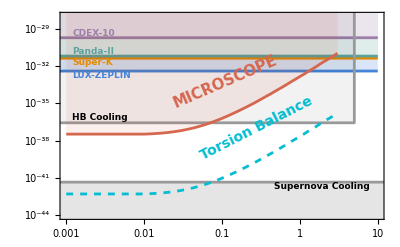

```mathematica
Show[
LogLogPlot[
{σLZ,σSK,σPandaX,σCDEX},{x,10^-4,10^1},
FrameLabel->frameLabel,
PlotRange->{{10^-3,10^1},{10^-44,10^-28}},
PlotStyle->{myColor2,myColor3,myColor4,myColor5},
Filling->{1->{1,Lighter[myColor2,0.8]},2->{1,Lighter[myColor3,0.8]},3->{1,Lighter[myColor4,0.8]},4->{1,Lighter[myColor5,0.8]}},
FrameTicks->{{leftTicks,rightTicks},{bottomTicks,topTicks}}
],
LogLogPlot[
{σSupernovaLower,σSupernovaUpper2},{x,10^-4,10^3},
PlotStyle->{GrayLevel[0.6]},
Filling->{1->{{2},Opacity[0.1]}}
],
ListLogLogPlot[
{{10^-4,σHB},{5,σHB},{5,1}},
Joined->True,
PlotStyle->{GrayLevel[0.6]},
Filling->{1->{1,Opacity[0.05]}}
],
ListLogLogPlot[limitMICROSCOPEMassinkeV[[;;-5]],PlotStyle->myColor1,Joined->True,Filling->1,FillingStyle->Opacity[0.1],PlotRange->{{All,3},All}],
ListLogLogPlot[limitProjTBMassinkeV2[[;;-5]],PlotStyle->{myColor6,Dashed},Joined->True],
(*ListLogLogPlot[limitAlPt1972MassinkeV,PlotStyle->myColor1,Joined->True,Filling->1],*)
Epilog->{
Inset[Rotate[myStyle["MICROSCOPE",15,myColor1,Bold],0.13π],Log/@{0.1,2 10^-33},{Center,Top}],
Inset[Rotate[myStyle["Torsion Balance",14,myColor6,Bold],0.15π],Log/@{0.25,3 10^-37},{Center,Top}],
Inset[Rotate[myStyle["LUX-ZEPLIN",9,myColor2,Bold],0.π],Log/@{0.0012,σLZ},{Left,Top}],
Inset[Rotate[myStyle["Super-K",9,myColor3,Bold],0.π],Log/@{0.0012,σSK},{Left,Top}],
Inset[Rotate[myStyle["Panda-II",9,myColor4,Bold],0.π],Log/@{0.0012,σPandaX},{Left,Bottom}],
Inset[Rotate[myStyle["CDEX-10",9,myColor5,Bold],0.π],Log/@{0.0012,σCDEX},{Left,Bottom}],
Inset[Rotate[myStyle["Supernova Cooling",9,Bold],0.π],Log/@{8,σSupernovaUpper2},{Right,Top}],
Inset[Rotate[myStyle["HB Cooling",9,Bold],0.π],Log/@{0.0012,1.2σHB},{Left,Bottom}]
}
]
```